# Exponente de Lyapunov

El exponente de Lyapunov, λ, es un parámetro que cuantifica qué tanto divergen dos órbitas infinitesimalmente cercanas.

-Graphics-
-Graphics-

## Para el mapeo logístico

El mapeo logístico es un mapeo discreto que es notable por su aparente simplicidad y complejidad de la dinámica. Está definido como un mapeo recurrente dado por

x_(n+1) = r x_n(1-x_n)

Esta ecuación implica que podemos definir el mapeo como una sucesión de aplicaciones de una función f(x_n) dada por

f(x_n) = r x_n(1-x_n)

donde la n-ésima iteración estará dada por una composición de n aplicaciones de la función f. Haciendo que r = 2, la dinámica con valor inicial x_0 = 0.23 durante  50 iteraciones es:

```mathematica
LogisticEquation[r_,x_]:=r x (1-x);
LogisticMap[r_,x0_,iter_]:=NestList[LogisticEquation[r,#]&,x0,iter];
```

```mathematica
LogisticMap[2,0.23,50]
```

{0.23,0.3542,0.457485,0.496385,0.499974,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5}

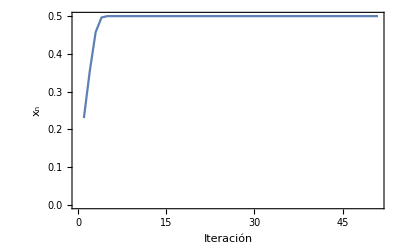

```mathematica
ListLinePlot[LogisticMap[2,0.23,50],Frame->True,FrameLabel->{"Iteración","x_n"}]
```

Haciendo lo mismo con r = 3

```mathematica
LogisticMap[3,0.23,50]
```

{0.23,0.5313,0.747061,0.566883,0.73658,0.58209,0.729784,0.591598,0.724829,0.598355,0.720979,0.603505,0.71786,0.607611,0.71526,0.61099,0.713044,0.613837,0.711123,0.616281,0.709436,0.618409,0.707938,0.620286,0.706594,0.621957,0.70538,0.623458,0.704275,0.624816,0.703263,0.626052,0.702333,0.627185,0.701472,0.628227,0.700674,0.62919,0.69993,0.630084,0.699234,0.630917,0.698582,0.631696,0.697969,0.632425,0.697391,0.633111,0.696845,0.633756,0.696328}

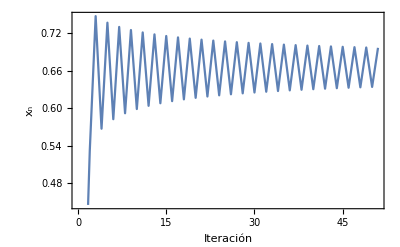

```mathematica
ListLinePlot[LogisticMap[3,0.23,50],Frame->True,FrameLabel->{"Iteración","x_n"}]
```

Con r = 4

```mathematica
LogisticMap[4,0.23,50]
```

{0.23,0.7084,0.826278,0.574171,0.977994,0.0860851,0.314698,0.862653,0.473933,0.997282,0.0108426,0.0429,0.164239,0.549057,0.990374,0.0381347,0.146722,0.500778,0.999998,9.68257×10^-6,0.0000387299,0.000154914,0.000619558,0.0024767,0.00988226,0.0391384,0.150426,0.511193,0.999499,0.00200349,0.00799789,0.0317357,0.122914,0.431225,0.98108,0.0742476,0.27494,0.797391,0.646234,0.914462,0.312884,0.85995,0.481743,0.998667,0.0053261,0.0211909,0.0829675,0.304335,0.846862,0.518748,0.998594}

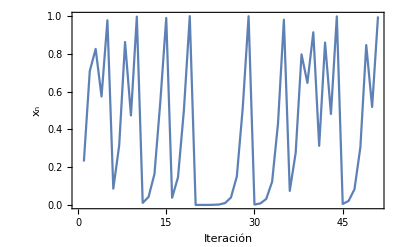

```mathematica
ListLinePlot[LogisticMap[4,0.23,50],Frame->True,FrameLabel->{"Iteración","x_n"}]
```

Podemos visualizar los puntos generados para r en el intervalo entre 2 y 4:

```mathematica
LogisticR[rmin_,rmax_,dr_]:=Flatten[Table[Thread[{r,LogisticMap[r,0.22,300]}],{r,rmin,rmax,dr}],1];
```

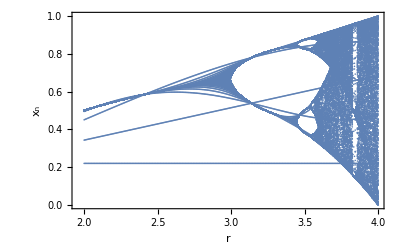

```mathematica
ListPlot[LogisticR[2,4,0.005],Frame->True,FrameLabel->{"r","x_n"}]
```

Podemos concluir que el tipo de dinámica depende del factor r. Intuitivamente podemos describir que la dinámica con r = 2 es convergente, r = 3 es periódica y r = 4 parece caótica. ¿Cómo podemos cuantificar el caos? Una manera de hacerlo es midiendo la distancia entre dos puntos inicialmente muy cercanos.

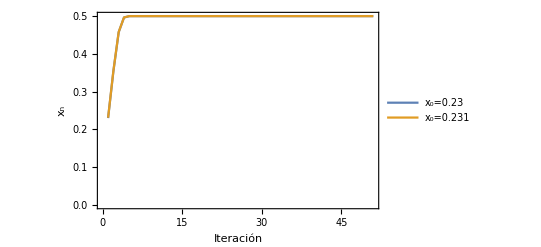

```mathematica
ListLinePlot[{LogisticMap[2,0.23,50],LogisticMap[2,0.231,50]},Frame->True,FrameLabel->{"Iteración","x_n"},PlotLegends->{"x_0=0.23","x_0=0.231"}]
```

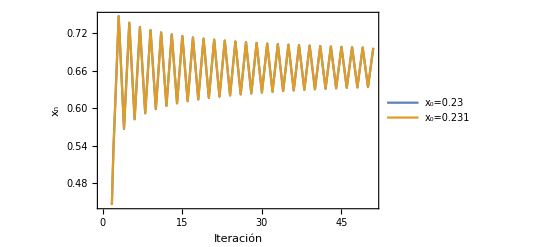

```mathematica
ListLinePlot[{LogisticMap[3,0.23,50],LogisticMap[3,0.231,50]},Frame->True,FrameLabel->{"Iteración","x_n"},PlotLegends->{"x_0=0.23","x_0=0.231"}]
```

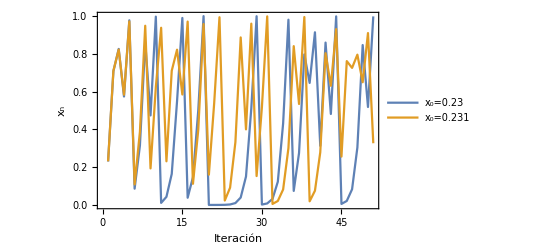

```mathematica
ListLinePlot[{LogisticMap[4,0.23,50],LogisticMap[4,0.231,50]},Frame->True,FrameLabel->{"Iteración","x_n"},PlotLegends->{"x_0=0.23","x_0=0.231"}]
```

El exponente de Lyapunov cuantifica qué tanto divergen dos puntos infinitesimalmente cercanos. Lo podemos calcular de la siguiente manera:

```mathematica
LogisticPrime[r_,x_]=Block[{xs},D[LogisticEquation[r,xs],xs]/.xs->x];
```

```mathematica
LyapunovLogistic[r_,x0_,iter_]:=Block[{logs,sum},
logs = Map[Log[Abs[LogisticPrime[r,#]]]&,LogisticMap[r,x0,iter]];
sum =Total[Drop[logs,1]];
Return[sum/Length[logs]];
];
```

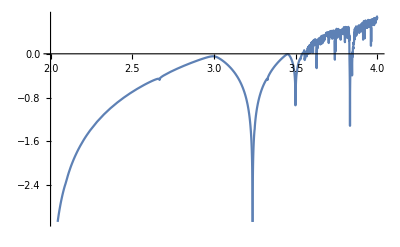

```mathematica
Plot[Lyapunov[r,0.25,100],{r,2,4}]
```

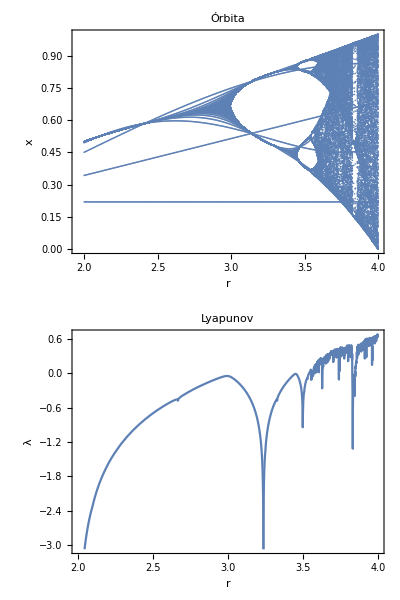

```mathematica
Column[
{
ListPlot[
LogisticR[2,4,0.005],
Frame->True,
FrameLabel->{"r","x"},
PlotLabel->"Órbita",
ImageSize->400
],
Plot[
Lyapunov[r,0.25,100],
{r,2,4},
Frame->True,
FrameLabel->{"r","λ"},
PlotLabel->"Lyapunov",
ImageSize->400
]
}
]
```

## Para el péndulo doble

```mathematica
SolveDPWithInitial[θ1Initial_,θ2Initial_,tMax_]:=Block[{m1=10.0,m2=5,l=20.0,g=9.81,θ1,θ2},
(* Solución numérica *)NDSolveValue[{θ1''[t]==(-g*( 2*m1+m2 )*Sin[θ1[t]]-m2*g*Sin[θ1[t]-2*θ2[t]]-2*Sin[θ1[t]-θ2[t]]*m2*( l*(θ2'[t]^2 )+( θ1'[t]^2 )*Cos[θ1[t]-θ2[t]] ))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])), θ2''[t]==(2*Sin[θ1[t]-θ2[t]]*(g*(m1+m2)*Cos[θ1[t]]+l*((θ2'[t]^2)*m2*Cos[θ1[t]-θ2[t]]+(θ1'[t]^2)*(m1+m2))))/(l*(2*m1+m2-m2*Cos[2*(θ1[t]-θ2[t])])),
θ1[0] == θ1Initial, θ2[0] == θ2Initial, θ2'[0] == 0, θ1'[0] == 0},{θ1,θ2},{t,0,tMax},AccuracyGoal->40,MaxSteps->10^6
]
];
```

```mathematica
Last[SolveDPWithInitial[1,0,200]]
```

InterpolatingFunction[…]

```mathematica
CalculateLyapunov[f_,xMin_,xMax_,Δx_]:=Block[{lyapunovPoints},
lyapunovPoints = DeleteCases[Table[Log[Abs[f'[t]]],{t,xMin,xMax,Δx}],Indeterminate];
Total[lyapunovPoints]/Length[lyapunovPoints]
];
```

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
λs = Flatten[
ProgressTable[
If[(θ1Initial ≠ 0 ||θ2Initial ≠ 0) && (θ1Initial ≠ θ2Initial),
{θ1Initial,θ2Initial,CalculateLyapunov[Last[SolveDPWithInitial[θ1Initial,θ2Initial,150]],0,150,0.05]},
Nothing
],
{θ1Initial,-3,3,0.1},{θ2Initial,-2,2,0.1}
],
1
];
```

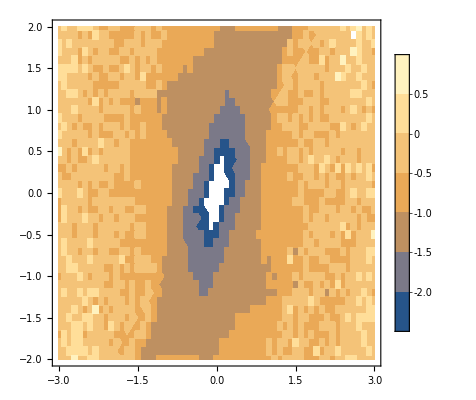

```mathematica
ListContourPlot[λs,InterpolationOrder->0,PlotLegends->Automatic]
```